### Parameters

```mathematica
chop[x_,a_,b_]:=Which[x>b,b,a≤x≤b,x,x<a,a] ; (*Energy store function*)

dynamicProgrammingClark[Tu_,Mu_, cu_, xcu_, betau_, alphau_, lambdau_, Yu_, x0u_] :=
Module[{T=Tu, M=Mu, c=cu, xc=xcu, beta=betau, alpha= alphau, lambda=lambdau, Y=Yu, x0=x0u},

α = alpha;
β = beta;
λ = lambda;

v=Table[0,{i,1,M}]; (* Store the patches survival probabilities on each iteration *)
d=Table[0,{i,1,c}];(* Store the optimal patch index *)
f1=Table[If[i≤xc,0,1 ],{i,c}]; (* Final survival proabilities *)
f0=Table[0,{i,c}]; (* Survival probability state *)
fall={}; (*Matrix to store all variable states*)
dall={}; (*Matrix to store all patch selections*)

For[t=T-1,t>0,t--, (* Times loop *)

For[x=xc+1,x≤ c,x++, (* Energy loop *)

For[j=1,j≤M,j++, (* Patches loop *)

(* Evaluate survival probability for each patch *)
v[[j]]=(1-β[[j]])(λ[[j]]f1[[chop[x-α[[j]]+Y[[j]],xc,c]]]+(1-λ[[j]])f1[[chop[x-α[[j]],xc,c]]])

];

v = Table[SetPrecision[v[[i]], 12], {i, 1, Length[v]}];

(* Get the maximum survival probability value for each energy level x *)
vm=Max[v]; 
(* Get the patch that maximizes survival, the optimal decision at time t, or each energy level x *)
d[[x]]=Position[v,vm][[1,1]];

(* Store the maximum survival probability value for each energy level x *)
f0[[x]]=SetPrecision[vm,12];

];

AppendTo[fall,f0]; (* Store the vector with the maximum survival probabilities at time t in the matrix fall *)
AppendTo[dall,d]; (* Store the vector with the optimal patch deicision at time t in the matrix dall *)

(* Update the survivial probabilities *)
f1=f0;
];

(* Maximum survival probability *)
fopt=Transpose[fall[[;;,xc+1;;c]]];
dopt=Transpose[dall[[;;,xc+1;;c]]]; 

(* Optimal patch selection *)
(* Single trajectory *)

xVector={x0}; (*State variable*)

fopttraj={}; (*Variable state*)
dopttraj={};(*Optimal patch index*)

ftest=Table[If[i≤xc,0,1 ],{i,c}];
t=1;

If[
ftest[[chop[Last[xVector],xc,c]]]==1,

While[t< T,

fopttraj=AppendTo[fopttraj,fopt[[Last[xVector]-xc,-t]] ];
dopttraj=AppendTo[dopttraj,dopt[[Last[xVector]-xc,-t]] ];

xVector=AppendTo[xVector,chop[Last[xVector]-α[[Last[dopttraj]]]+Y[[Last[dopttraj]]],xc,c]];

t=t+1];
];

Return[{xVector,fopttraj,dopttraj}]
];
```

{7,6,5,8,7,6,5,8,7,6,5,8,7,10,10,9,10,9,8,7}

{0.007145,0.0080172,0.0092345,0.018958,0.021311,0.024523,0.028638,0.058793,0.064758,0.075916,0.083839,0.17212,0.18457,0.37892,0.52808,0.63702,1.,1.,1.}

{1,1,5,1,1,1,5,1,1,1,5,1,5,5,1,3,1,1,1}

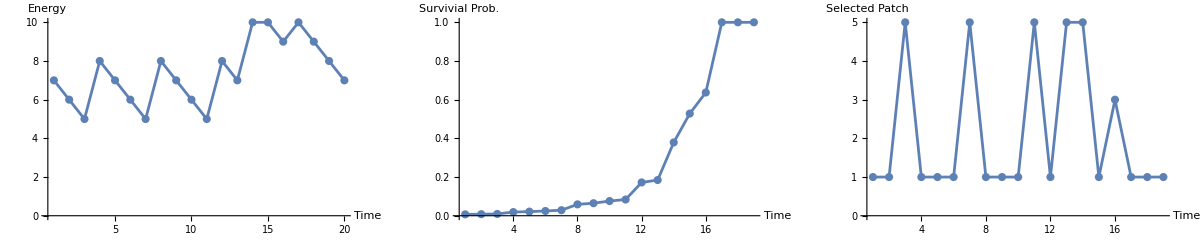

```mathematica
(* Running an example [from Clark]
Original patch example in Baltazar Code *)
T=20; (* Iterations *)
c=10; (* Maximum energy *)
xc=3; (* Minimum energy for survival *)

(* Example from Clark*)
(*M= 3;
β={0,0.004,0.02}; 
α={1,1,1}; 
λ={0,0.4,0.6};
Y={0,3,5}; 
x0=4;*)

(* My example *)

(*M = 5;
α={2,3,4,5,6};
β = {0,0,0,0,0};
λ ={0.5,1,1,1,1};
Y = {1,3,5,7,9};
x0= 7;*)

(* Another example 

"Parameters to use:"{2,3,4,5,6}{0,0,0,0,0}{0.1156440905853021867`4.,0.2312881811706043733`4.,0.3469322717559066294`4.,0.4625763623412087466`4.,0.5782204529265109194`4.}{1,3,5,7,9}"x0: "10 *)

M= 5;
α = {2,3,4,5,6};
β = {0,0,0,0,0};
λ = {0.0974,0.1949,0.2923,0.3897,0.4871};
Y = {1,3,5,7,9};
x0 = 7;

{x1,x2,x3}= dynamicProgrammingClark[T,M,c,xc,β,α,λ,Y,x0];
Print[x1];
Print[x2];
Print[x3];
GraphicsRow[{ListLinePlot[x1,AxesLabel-> {"Time","Energy"},LabelStyle->Directive[Bold,12],ImageSize->300,PlotRange->All,Mesh->All],
ListLinePlot[x2,AxesLabel-> {"Time","Survivial Prob."},LabelStyle->Directive[Bold,12],ImageSize->300,PlotRange->All,Mesh->All],
ListLinePlot[x3,AxesLabel-> {"Time","Selected Patch"},LabelStyle->Directive[Bold,12],ImageSize->300,PlotRange->All,Mesh->All]}]
```

```mathematica
T=20; (* Iterations *)
c=10; (* Maximum energy *)
xc=3; (* Minimum energy for survival *)
M= 5;
α = {2,3,4,5,6};
β = {0,0,0,0,0};
λ = {0.0974,0.1949,0.2923,0.3897,0.4871};
Y = {1,3,5,7,9};
x0 = 7;

v=Table[0,{i,1,M}]; (* Store the patches survival probabilities on each iteration *)
d=Table[0,{i,1,c}];(* Store the optimal patch index *)
f1=Table[If[i≤xc,0,1 ],{i,c}]; (* Final survival proabilities *)
f0=Table[0,{i,c}]; (* Survival probability state *)
fall={}; (*Matrix to store all variable states*)
dall={}; (*Matrix to store all patch selections*)

For[t=T-1,t>0,t--, (* Times loop *)

For[x=xc+1,x≤ c,x++, (* Energy loop *)

For[j=1,j≤M,j++, (* Patches loop *)

(* Evaluate survival probability for each patch *)
v[[j]]=(1-β[[j]])(λ[[j]]f1[[chop[x-α[[j]]+Y[[j]],xc,c]]]+(1-λ[[j]])f1[[chop[x-α[[j]],xc,c]]])

];

v = Table[SetPrecision[v[[i]], 10], {i, 1, Length[v]}];

(* Get the maximum survival probability value for each energy level x *)
vm=Max[v]; 
(* Get the patch that maximizes survival, the optimal decision at time t, or each energy level x *)
d[[x]]=Position[v,vm][[1,1]];

(* Store the maximum survival probability value for each energy level x *)
f0[[x]]=SetPrecision[vm,10];

];

AppendTo[fall,f0]; (* Store the vector with the maximum survival probabilities at time t in the matrix fall *)
AppendTo[dall,d]; (* Store the vector with the optimal patch deicision at time t in the matrix dall *)

(* Update the survivial probabilities *)
f1=f0;
];

Print["======"];
(* Maximum survival probability *)
fopt=Transpose[fall[[;;,xc+1;;c]]];
dopt=Transpose[dall[[;;,xc+1;;c]]]; 

Print[fopt];
Print["---"];
Print[dopt];
```

```mathematica
(* Optimal patch selection *)
(* Single trajectory *)

xVector={x0}; (*State variable*)

fopttraj={}; (*Variable state*)
dopttraj={};(*Optimal patch index*)

ftest=Table[If[i≤xc,0,1 ],{i,c}];
t=1;

If[
ftest[[chop[Last[xVector],xc,c]]]==1,

While[t< T,

Print["Ah: ", Last[xVector]-xc];

val1 = fopt[[Last[xVector]-xc,-t]];
val2 = dopt[[Last[xVector]-xc,-t]] ;

Print["t=", t, ", v1=", val1, ",v2=", val2]; 

fopttraj=AppendTo[fopttraj, val1];
dopttraj=AppendTo[dopttraj,val2];

Print["valsuse: ", Last[xVector],", ",Last[dopttraj],"| ", α[[Last[dopttraj]]],", ", Y[[Last[dopttraj]]]];

valappend = chop[Last[xVector]-α[[Last[dopttraj]]]+Y[[Last[dopttraj]]],xc,c];
Print["vappend=", valappend];
xVector=AppendTo[xVector,valappend];

t=t+1];
];
xVector
```

{7,6,5,8,7,6,5,8,7,6,5,8,7,10,10,9,10,9,8,7}

```mathematica
(* Functions for the adaptive logistic regression *)

solveLogisticSystem[p0u_,t0u_,t1u_,ku_, ru_]:=
Module[{p0=p0u,t0=t0u,t1=t1u,  k=ku, r=ru},
Return[(k*p0*Exp[r*(t1-t0)])/(k+p0*(Exp[r*(t1-t0)]-1))];
];

findParams1[Mu_,p0u_,ku_,ftcostu_,ftpropfindfoodu_,vdigu_] :=
Module[{M=Mu, p0=p0u, k=ku, ftcost=ftcostu, ftpropfindfood=ftpropfindfoodu, vdig=vdigu},

(* See these parameters *)
beta0 = Table[0,{i,M}];alpha0= Table[IntegerPart[ftcost*i] + 1,{i,1,M}];
lambda0= Table[SetPrecision[chop[(ftpropfindfood*i)*(k/p0), 0, 1], 4],{i,1,M}];
YY0 = Table[IntegerPart[vdig*i],{i,1, 2*(M-1)+1, 2}];

Return[{beta0,alpha0, lambda0, YY0}]
];

findEnergyDynamic[tu_, p0u_,ku_, estartu_,paramsu_] :=
Module[{ t= tu,p0=p0u, k=ku, estart=estartu, params=paramsu},

T = params[[1]];
M= params[[2]];
c = params[[3]];
xc = params[[4]];
ftcost = params[[5]];
ftpropfindfood = params[[6]];
vdig = params[[7]];

{beta1, alpha1,lambda1,Y1} = findParams1[M,p0, k,ftcost,ftpropfindfood,vdig];

finalEnergyDay = estart;
finalForagingDay = 0;
xvector = {estart};

(* There is something wrong with this function call [Numeric] :/ *)
{xvector, fopttraj, dopttraj} = dynamicProgrammingClark[T, M, c, xc, beta1, alpha1, lambda1, Y1, estart];

graphUse =GraphicsRow[{ListLinePlot[xvector,AxesLabel-> {"Time","Energy"},LabelStyle->Directive[Bold,12],ImageSize->300,PlotRange->All,Mesh->All],
ListLinePlot[fopttraj,AxesLabel-> {"Time","Survivial Prob."},LabelStyle->Directive[Bold,12],ImageSize->300,PlotRange->All,Mesh->All],
ListLinePlot[dopttraj,AxesLabel-> {"Time","Selected Patch"},LabelStyle->Directive[Bold,12],ImageSize->300,PlotRange->All,Mesh->All]}];

If[Length[xvector]>1,
finalEnergyDay = xvector[[2]];
finalForagingDay = dopttraj[[2]];
];

Return[{finalEnergyDay, finalForagingDay, graphUse}]
];

adaptiveLogistic[p0u_,ku_, tmaxu_, estartu_,rcu_, paramsu_, adaptiveu_] :=
Module[{ p0=p0u, k=ku, tmax=tmaxu, estart=estartu, rc=rcu, params=paramsu, adaptive=adaptiveu},

pVector = {p0};
energyDay = estart;
rday = rc*estart;
energyVector = {};
rVector = {};
foragingVector = {};
graphsVector = {};

Do[

(*Solve the logistic for one day *)
pLast = Last[pVector];
pRangeDay = solveLogisticSystem[pLast ,t,t+1,k, rday];
AppendTo[pVector, pRangeDay];

If[adaptive,

(* Obtain new energy consumption for this day using dynamic programming *)
{energyDay1, foragingDay1, graphUse} = findEnergyDynamic[t,pLast ,k, energyDay ,params]; 

energyDay  = energyDay1;
foragingDay = foragingDay1;

(*Change the growth rate using this new energy*)
rday = rc*energyDay;

(*Append energy, growth rate and foraging time to corresponding vectors*)
AppendTo[rVector ,rday];
AppendTo[energyVector ,energyDay];
AppendTo[foragingVector ,foragingDay];
AppendTo[graphsVector,graphUse];
,0
];

, {t, tmax}];

Return[{pVector, energyVector, rVector, foragingVector, graphsVector}];
];
```

starting r 0.035

0.02>= 0.05: False

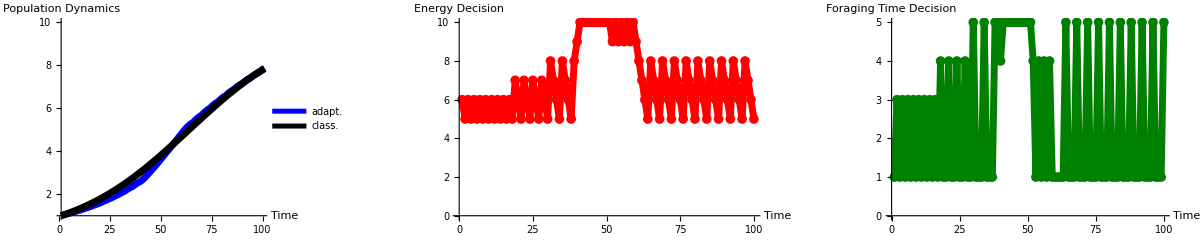
Prob find food = 0.05,  0.005, M = 5, T = 20, c = 10, xc = 3, e_start = 7.
-Graphics-

```mathematica
(* Example ---> *)
(* Logistic regression params *)
p0=1;
k = 10;
tmax=100;
estart=7;
rc = 0.005;
(* Dynamic programming params *)
Tuse=20;
M=5; 
c=10;
xc=3;
ftcost = 1; (* Energy cost for foraging time *)
ftprobfindfood = 0.05; (* Prob of finding food for foraging time *)
Print["starting r ",rc*estart]; 

Print[1./(k*M), ">= ", ftprobfindfood,": ", (1./(k*M))>= ftprobfindfood];
vdig = 1; (* digestion velocity *)
params = {Tuse,M,c,xc,ftcost, ftprobfindfood,vdig};
(* ==== *)
{pVector0, energyVector0, rVector0, foragingVector0, graphsVector0} =adaptiveLogistic[p0,k, tmax, estart,rc, params, False];
{pVector, energyVector, rVector, foragingVector, graphsVector} =adaptiveLogistic[p0,k, tmax, estart,rc, params, True];

title = "Prob find food = " <> ToString[ftprobfindfood] <> ",  " <> ToString[rc]<> ", M = "<>ToString[ M] <> ", T = " <> ToString[Tuse] <> ", c = " <> ToString[c] <> ", xc = " <> ToString[xc] <> ", e_start = " <> ToString[estart] <>".";

plott = Framed[
Column[{Style[title,Darker@Blue,Bold,12],

GraphicsRow[{
ListLinePlot[ {pVector, pVector0},
PlotStyle->{ 
Directive[Thickness[0.01],ToColor[RGBColor["blue"],Hue]],
Directive[Thickness[0.01],ToColor[RGBColor["black"],Hue]]
},
PlotRange->{{1,tmax},{1, k}},

PlotLegends->Placed[{
Style["adapt.",FontFamily->"Century",10],
Style["class.",FontFamily->"Century",10]
}, {Right,Top}],

AxesLabel-> {"Time","Population Dynamics"},
ImageSize->500],
ListLinePlot[energyVector,AxesLabel-> {"Time","Energy Decision"},LabelStyle->Directive[Bold,10],ImageSize->500,PlotRange->All,Mesh->All,
PlotStyle->{ 
Directive[Thickness[0.01],ToColor[RGBColor["red"],Hue]]
}],
ListLinePlot[foragingVector,AxesLabel-> {"Time","Foraging Time Decision"},LabelStyle->Directive[Bold,10],ImageSize->500,PlotRange->All,Mesh->All,
PlotStyle->{ 
Directive[Thickness[0.01],ToColor[RGBColor["green"],Hue]]
}]}]
},
Alignment->Center],
FrameMargins->10];
Export["C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/adaptive_logistic/plots/logistic_M_" <> ToString[M]<>"_plot_pfindfood"<>ToString[ftprobfindfood] <>"_rc"<>ToString[rc]<>"_T"<>ToString[Tuse]<>".png",plott,"PNG"];
plott
```